```mathematica
made by dr. xie in caojiabao
```

```mathematica
1.（1）空格或者*3表示乘法;（2）两个等式相连(==)表示等于;（3）输入括号、逗号等要记得调为英文输入法;（4）不能在算式内输入方括号
```

```mathematica
2.shfit+enter运行
```

```mathematica
3.希腊字母：插入->特殊字符
```

```mathematica
4.公式编辑：面板->数学助手
```

```mathematica
5.化简：Simplify和FullSimplify
```

```mathematica
6.放大缩小界面：ctrl+鼠标滑动
```

```mathematica
7.多项式降次序：Collect[f(x),x]
```

```mathematica
8.求导：D[f(x),x]
```

```mathematica
9.求方程的解：Solve[f(x)==0,x];求方程组的解Solve[ f(x)==0 &&g(y)==0,{x,y}]
```

```mathematica
10.可以同时进行多步骤求解：FullSimplify[Solve[D[f(x),x]==0,x]];Solve[D[f(x)==0,x]&&D[g(y)==0,y],{x,y}]
```

```mathematica
11.比较，求范围：Reduce[{f(x)>0,约束条件1，约束条件2，...},x]
```

```mathematica
12.代入化简/代入数值：FullSimplify[f(x,y)/.x->r*Subscript[A, H]+(1-r)*Subscript[A, L]/.y->θ*(Subscript[A, L]-c)+c]
```

```mathematica
13.求积分：直接从面板,课堂助手获得积分符号，输入公式即可
```

```mathematica
14.绘图：Plot[f(x),{x,min,max}]
```

```mathematica
15.数值解:N[任意数值]
```

```mathematica
16.合并：Together[]
```

```mathematica
17.快捷键：（插入->排版）上标：ctrl+6;下标：ctrl+-;分式：ctrl+?;箭头：->;希腊字母：esc+a;上杠：ctrl+7;下杠：ctrl+4;根式：ctrl+2
```

```mathematica
18.公式导出到word：方法一：直接复制到word,不能直接复制到wps;方法二：复制为mathml格式，粘贴到mathtype（该软件只有30天试用，最好找盗版）,修改再复制粘贴到word或wps
```

```mathematica
19.动态参数图:Manipulate[ParametricPlot[{x=r,y=f(x,c,b)},{r,0.1,1}],{c,0,1},{b,1.1,10}]
```

```mathematica
20.注释：alt+?
```

```mathematica
21.终止计算：alt+.
```

```mathematica
22.且&&，或||
```

```mathematica
23.遇到某些问题可能是软件问题，可将公式复制到另一个新文件运行或重新打开文件或重启软件（一般都是自己输入错误，或者公式错误，或者受前面输入的影响）
```

```mathematica
24.选中"命令"，F1键可查看官方文档
```

```mathematica
25.%n(n为之前的out)可直接调用之前的out(缺点：以后打开可能找不到%n)
```

```mathematica
FullSimplify[2*x^2+2*x+1]
```

```mathematica
26.遇到无法计算的式子
```

```mathematica
(1)遇到无法比较得出的结果的式子，可以尝试先使用其他的参数进行比较，然后再用自己想要用的参数进行进一步计算。
```

```mathematica
(2)
```

```mathematica
27.判断式子正负FullSimplify[(a+b)/c>0,{a>c>0,b>0}],慎用该公式，在第二选项{}里，建议不要用互相冲突的约束，否则，该算式自动选择使得等式成立的约束。具体请检索"带有假定的化简"
```

```mathematica
28.判断式子结果取值情况（待研究），f[a_,r_,t_]=1/(2-(1+r) t)-(2 (-1+r) (a+(-2+a) t)^2)/(4 a^2 (-1+r)+a^3 (1+r) (8-8 r+a (-5+3 r))+a (-16 (-1+r)+a (-5+6 r-5 r^2)) t+(-16+5 a+a^2+2 (8-7 a+3 a^2) r+(13-3 a) a r^2) t^2);data=RandomReal[{0,1},{1000,3}];
{data,f@@@data}//Transpose//TableForm[#,TableHeadings->{None,{"a,r,t 取值","f 取值"}}]&
```

```mathematica
29.求最大最小值：Minimize，Maximize；Maximize[{f(x),1>=x>=0},x]
```

```mathematica
30.Factor[],将一个式子分解成几个因式的乘积。
```

```mathematica
31.带条件展开公式：FullSimplify[(AH/(AH-AL)-2 √2 √(-(-8 i+3 b^2 i)/((AH-AL)^2 (16-16 b+5 b^2))))^2,AH>AL]//Expand
```

```mathematica
32.绝对值计算：Abs[-1]
```

```mathematica
33.快捷命令 Numerator[((128+b (-128+16 b+9 b^3)) d+b (-128+112 b-9 b^3) α)^2]~Collect~b
```

```mathematica
34.Cancel[(x^2-1)/(x-1)]
```

```mathematica
35.Solve[x^2-4==0&&x>0,x]
```

```mathematica
Solve[x^2-4==0&&x>0,x]
```

{{x→2}}

```mathematica
36.Tooltip的使用
```

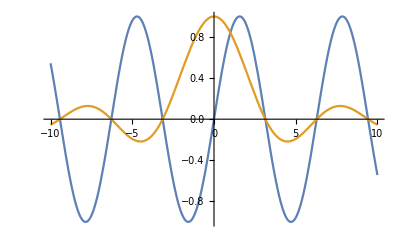

```mathematica
Plot[Tooltip[{Sin[x],Sin[x]/x}],{x,-10,10}]
```

```mathematica
37.带条件化简：FullSimplify[(AH/(AH-AL)-2 √2 √(-(-8 i+3 b^2 i)/((AH-AL)^2 (16-16 b+5 b^2))))^2,Assumptions->{AH>AL>0}]
```

```mathematica
38.FullSimplify[x]等价于 x//FullSimplify
```

```mathematica
39.FullSimplify[a x^2+b x+ c x^2]//Collect[#,x]&
```

```mathematica
FullSimplify[a x^2+b x+ c x^2]//Collect[#,x]&
```

b x+(a+c) x^2

```mathematica
FullSimplify[(AH/(AH-AL)-2 √2 √(-(-8 i+3 b^2 i)/((AH-AL)^2 (16-16 b+5 b^2))))^2,Assumptions->{AH>AL>0}]
```

((AH-2 √2 √(((8-3 b^2) i)/(16+b (-16+5 b))))^2)/(AH-AL)^2

```mathematica
FullSimplify[(AH/(AH-AL)-2 √2 √(-(-8 i+3 b^2 i)/((AH-AL)^2 (16-16 b+5 b^2))))^2,AH>AL]
```

((AH-2 √2 √(((8-3 b^2) i)/(16+b (-16+5 b))))^2)/(AH-AL)^2

```mathematica
40.同时化简代入多个同样的参数值FullSimplify[{w*qr+w*qe+δ/2*(qr+qe)^2,(a-qr-t*qe-w)*qr}/.qr->(a-w)/(2+t)/.qe->(a-w)/(2+t)/.w->(a (2+t-2 δ))/(2 (2+t-δ))]
```

```mathematica
问题：
```

```mathematica
1.Root[-1-12#1-34#1^2-30#1^3&,1]是什么意思
```

```mathematica
1-12#1-34#1^2-30#1^3&表示某函数，你可以看看Mathematica的函数式语法。方程的根无法给出精确值的时候Mathematica就会用Root表示，表示某方程的第k个根。如果要数值解，可以直接N[Root[-1-12#1-34#1^2-30#1^3&,1]]
```

```mathematica
N[Root[1-y+#1^4+#1^5&,1]]
```

-1.40764

```mathematica
Collect[1/96 ((-4 c+u)^2+3 Subscript[A, H] (8 c (-2+r)+2 r u+3 r^2 Subscript[A, H])-6 (-1+r) (4 c+u+3 r Subscript[A, H]) Subscript[A, L]+9 (-1+r)^2 Subscript[A, L]^2),c]
```

1/96 c (24 (r-2) A_H-24 (r-1) A_L-8 u)+1/96 (-18 (r-1) r A_H A_L+9 r^2 A_H^2+6 r u A_H-6 (r-1) u A_L+9 (r-1)^2 A_L^2+u^2)+c^2/6

```mathematica
D[2*x^2+2*x+1,x]
```

2+4 x

```mathematica
Solve[2*x^2+2*x+1==0,x]
```

{{x→-1/2-ⅈ/2},{x→-1/2+ⅈ/2}}

```mathematica
Solve[1/96 ((-4 c+u)^2+3 Subscript[A, H] (8 c (-2+r)+2 r u+3 r^2 Subscript[A, H])-6 (-1+r) (4 c+u+3 r Subscript[A, H]) Subscript[A, L]+9 (-1+r)^2 Subscript[A, L]^2)==0,c]
```

{{c→1/4 (u+6 A_H-3 r A_H-3 A_L+3 r A_L-2 √3 √(u A_H-r u A_H+3 A_H^2-3 r A_H^2-u A_L+r u A_L-3 A_H A_L+3 r A_H A_L))},{c→1/4 (u+6 A_H-3 r A_H-3 A_L+3 r A_L+2 √3 √(u A_H-r u A_H+3 A_H^2-3 r A_H^2-u A_L+r u A_L-3 A_H A_L+3 r A_H A_L))}}

```mathematica
FullSimplify[Solve[D[2*x^2+2*x+1,x]==0,x]]
```

{{x→-1/2}}

```mathematica
Reduce[2*c^2+2*c>0,c]
```

c<-1||c>0

```mathematica
Reduce[{FullSimplify[1/8 (4 c+u+3 r Subscript[A, H]-3 (-1+r) Subscript[A, L])/.u->r*Subscript[A, H]+(1-r)*Subscript[A, L]/.Subscript[A, H]->θ*(Subscript[A, L]-c)+c]>0,0<r<1,θ>1,0<c<Subscript[A, L]},θ]
```

A_L>0&&0<c<A_L&&0<r<1&&θ>1

```mathematica
FullSimplify[1/8 (4 c+u+3 r Subscript[A, H]-3 (-1+r) Subscript[A, L])/.u->r*Subscript[A, H]+(1-r)*Subscript[A, L]/.Subscript[A, H]->θ*(Subscript[A, L]-c)+c]
```

1/2 (c (1+r-r θ)+(1+r (-1+θ)) A_L)

```mathematica
2*x^2+2*x
```

```mathematica
x==2*y+1
```

```mathematica
FullSimplify[2*x^2+2*x/.x->2*y+1]
```

4 (1+y) (1+2 y)

```mathematica
∫_1^2 xⅆx
```

3/2

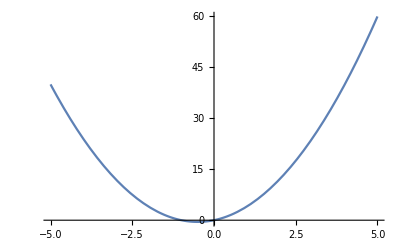

```mathematica
Plot[2*x^2+2*x,{x,-5,5}]
```

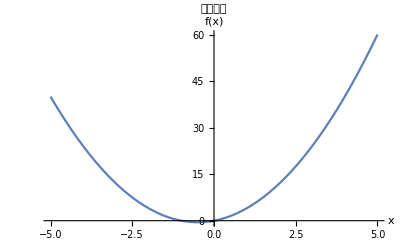

```mathematica
Show[%17,AxesLabel->{HoldForm[x],HoldForm[f [x]]},PlotLabel->HoldForm[求最小值],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Show[%22,AxesStyle->Gray]
```

```mathematica
Manipulate[ParametricPlot[{x=r,y=(-16 c+8 c r+5 c r^2+8 r b-5 r^2 b)/(5 c r^2-5 r^2 b)},{r,0.1,1}],{c,0,1},{b,1.1,10}]
```

```mathematica
N[√2]
```

1.41421

```mathematica
N[√2,10]
```

1.414213562

```mathematica
问题：
```

```mathematica
为什么这个约不掉
```

```mathematica
Simplify[(√2 √(k (5 p β^2+2 k (-1+p+Q β)^2)))/(5 k β)-1/5 √((10 p β^2+4 k (-1+p+Q β)^2)/(k β^2)) ]
```

```mathematica
26.(1)例子
```

```mathematica
Reduce[{1/(6250 p β^4)(-3 (-3+3 p+3 Q β-β √((10 p β^2+4 k (-1+p+Q β)^2)/(k β^2))) (-10 p β^2+k (-1+p+Q β) (-2+2 p+2 Q β+β √((10 p β^2+4 k (-1+p+Q β)^2)/(k β^2))))^2+(4 (2 k^2 (-1+p+Q β)^3+10 √2 p β^2 √(k (5 p β^2+2 k (-1+p+Q β)^2))+k (-1+p+Q β) (√2 (-1+Q β) √(k (5 p β^2+2 k (-1+p+Q β)^2))+p (-40 β^2+√2 √(k (5 p β^2+2 k (-1+p+Q β)^2)))))^2)/(k (3 k (-1+p+Q β)-√2 √(k (5 p β^2+2 k (-1+p+Q β)^2)))))>0,0<p<1,β>0,k>0,Q>0},k]
```

```mathematica
Reduce[{β>0&&0<p<1&&Q>(1-p)/β&&k>(2 p β^2)/(1-2 p+p^2-2 Q β+2 p Q β+Q^2 β^2),0<p<1,β>0,k>0,Q>0},β]
```

```mathematica
27.例子
```

```mathematica
FullSimplify[((-1+α) α (a-c+α m))/(-4+2 α (2+α (-1+β)))-(2 (-1+α) α (a-c+α m))/(-4+α (4+α (-3+4 β)))>0,{a>c>0,((-1+α) α (a-c+α m))/(-4+2 α (2+α (-1+β)))>0,(2 (-1+α) α (a-c+α m))/(-4+α (4+α (-3+4 β)))>0,c>m>0,c>0,1>β>0,1>α>0}]
```

α (4+α (-3+4 β))>4

```mathematica
FullSimplify[((-1+α) α (a-c+α m))/(-4+2 α (2+α (-1+β)))-(2 (-1+α) α (a-c+α m))/(-4+α (4+α (-3+4 β)))>0,{a>c>0,4+α^2 (3-4 β)<4 α,((-1+α) α (a-c+α m))/(-4+2 α (2+α (-1+β)))-(2 (-1+α) α (a-c+α m))/(-4+α (4+α (-3+4 β)))>0,c>m>0,c>0,1>β>0,1>α>0}]
```

True

```mathematica
Reduce[{((-1+α) α (a-c+α m))/(-4+2 α (2+α (-1+β)))-(2 (-1+α) α (a-c+α m))/(-4+α (4+α (-3+4 β)))>0,a>c>0,((-1+α) α (a-c+α m))/(-4+2 α (2+α (-1+β)))>0,(2 (-1+α) α (a-c+α m))/(-4+α (4+α (-3+4 β)))>0,c>m>0,c>0,1>β>0,1>α>0},{α}]
```

False

```mathematica
29.
```

```mathematica
Factor[α (4 a-4 c+8 m+8 w-4 a α+4 c α-4 w α-3 a α^2+3 c α^2-2 m α^2+2 w α^2+3 w α^3-16 m α β-16 w α β+16 a α^2 β-16 c α^2 β+8 m α^2 β+8 w α^2 β-16 w α^3 β-16 a α^2 β^2+16 c α^2 β^2+16 w α^3 β^2)]
```

α (-2-α+4 α β) (-2 a+2 c-4 m-4 w+3 a α-3 c α+2 m α+4 w α-3 w α^2-4 a α β+4 c α β+4 w α^2 β)